```mathematica
psize=.05;
lthick=.01;
arrlng=.2;
points={{0,0},{-1,0},{-1,-1},{0,-1},{0,0}};
pointsr=Table[{points[[q,2]],points[[q,1]]},{q,Length[points]}];
boxpos={{0,0},{2,1},{-1,2},{-2,-1},{1,-2}};
vacr={{1,0},{-1,1},{-2,-1},{0,-2}};
vac=Table[{vacr[[q,2]],vacr[[q,1]]},{q,Length[vacr]}]
vacc[pnt_]:={Green,Table[Rectangle[pnt[[q]]-1.5*psize,pnt[[q]]+1.5*psize],{q,Length[pnt]}]};
boxposr=boxpos;
boxposr[[1]]=boxpos[[1]];
(*Table[boxposr[[q]]={boxpos[[Length[boxpos]+1-q,2]],boxpos[[Length[boxpos]+1-q,1]]},{q,2,Length[boxpos]}];*)
Table[boxposr[[q]]={boxpos[[q,2]],boxpos[[q,1]]},{q,2,Length[boxpos]}];
lines={{{0,0},{1,0}},{{-1,0},{-1,1}},{{-1,-1},{-2,-1}},{{0,-1},{0,-2}}};
box[x_,y_]:={Thickness[lthick],Line[Table[x[[q]]+y,{q,Length[x]}]]};
J1p[pnt_,bx_]:={Dashing[None],Red,Thickness[lthick],Table[Table[Line[{pnt[[q]]+bx[[p]],bx[[p]]+pnt[[1+Mod[q+1,4]]]+bx[[q+1]]}],{q,Length[pnt]-1}],{p,Length[bx]}]};
J1[pnt_,bx_]:={Blue,Dashing[None],Thickness[lthick],Table[Table[box[Table[pnt[[n]]+bx[[p]],{n,Length[pnt]}],bx[[q]]],{p,Length[bx]}],{q,Length[bx]}]};

J2p[pnt_,bx_]:={Dashed,Red,Thickness[lthick],Table[Table[Line[{pnt[[q]]+bx[[p]]+bx[[n]],bx[[p]]+pnt[[1+Mod[q,Length[pnt]]]]+bx[[q+1]]+bx[[n]]}],{q,Length[pnt]-1},{n,Length[pnt]}],{p,Length[bx]}]};

J2[pnt_,bx_]:={Blue,Dashed,Thickness[lthick],Table[Table[Line[{pnt[[q]]+bx[[p]],pnt[[1+Mod[q+2,Length[pnt]]]]+bx[[p]]}],{p,Length[bx]}],{q,Length[bx]}]};

(*Stuff for J3*)
f[t_]:={Cos[t]/(2*Cos[Pi/4]),Sin[t]-Sin[Pi/4]}
f2[t_]:={Cos[t+Pi/2]/(2*Cos[Pi/4])-Cos[Pi/4+Pi/2]/(2*Cos[Pi/4]),Sin[t+Pi/2]/(2*Sin[Pi/4])};
f3[t_]:={Cos[t+Pi]/(2*Cos[Pi/4]),Sin[t+Pi]-Sin[Pi/4+Pi]}
f4[t_]:={Cos[t-Pi/2]/(2*Cos[Pi/4])-Cos[Pi/4-Pi/2]/(2*Cos[Pi/4]),Sin[t-Pi/2]/(2*Sin[Pi/4])};
darc[fun_,pnt1_,pnt2_]:=Table[fun[t]*{Max[Abs[pnt2[[1]]-pnt1[[1]]],1],Max[Abs[pnt2[[2]]-pnt1[[2]]],1]}+psel[pnt2,pnt1],{t,Pi/4,3Pi/4,.01}];
ps[pnt1_,pnt2_]:=Table[If[(pnt1-pnt2)[[n]]>0,1,If[(pnt1-pnt2)[[n]]<0,-1,0]],{n,2}]
options={{2,0},{0,2},{-2,0},{0,-2}};
dtst[pnt1_,pnt2_]:=Total[Table[Boole[pnt1-pnt2==options[[nn]]],{nn,Length[options]}]]>0;
dsel[pnt1_,pnt2_]:=
Switch[ps[pnt1,pnt2],{1,0},f,{0,1},f2,{-1,0},f3,{0,-1},f4];
psel[pnt1_,pnt2_]:=Switch[ps[pnt1,pnt2],{1,0},{Mean[{pnt1[[1]],pnt2[[1]]}],pnt1[[2]]},{0,1},{pnt1[[1]],Mean[{pnt1[[2]],pnt2[[2]]}]},{-1,0},{Mean[{pnt1[[1]],pnt2[[1]]}],pnt1[[2]]},{0,-1},{pnt1[[1]],Mean[{pnt1[[2]],pnt2[[2]]}]}];
pdarc[pnt1_,pnt2_]:=If[dtst[pnt1,pnt2],Line[darc[dsel[pnt1,pnt2],pnt1,pnt2]],##&[]];
pdarcr[pnt1_,pnt2_]:=If[dtst[pnt1,pnt2],Line[darc[dsel[pnt2,pnt1],pnt1,pnt2]],##&[]];
J3[pnt_,bx_]:={Black,Dashing[None],Thickness[lthick],Table[Table[pdarc[pnt[[q]]+bx[[n]],bx[[1+Mod[p+1,Length[bx]]]]+bx[[n]]+pnt[[1+Mod[2+q,Length[pnt]-1]]]],{q,Length[pnt]-1},{n,Length[pnt]-1}],{p,Length[bx]}]}
J3r[pnt_,bx_]:={Black,Dashing[None],Thickness[lthick],Table[Table[pdarcr[pnt[[q]]+bx[[n]],bx[[1+Mod[p+1,Length[bx]]]]+bx[[n]]+pnt[[1+Mod[2+q,Length[pnt]-1]]]],{q,Length[pnt]-1},{n,Length[pnt]-1}],{p,Length[bx]}]}


J3p[pnt_,bx_]:={Thickness[lthick],Black,Dashed,Table[Table[If[dtst[pnt[[q]]+bx[[n]],bx[[1+Mod[p+2,Length[bx]]]]+bx[[n]]+pnt[[1+Mod[2+q,Length[pnt]-1]]]],Line[{pnt[[q]]+bx[[n]],bx[[1+Mod[p+2,Length[bx]]]]+bx[[n]]+pnt[[1+Mod[2+q,Length[pnt]-1]]]}],##&[]],{q,Length[pnt]-1},{n,Length[pnt]-1}],{p,Length[bx]}]}

darrow[pnt_]:={Orange,PointSize[psize],Point[pnt],Black,Thickness[lthick],Line[{pnt-1.5*psize,pnt+1.5*psize}],Line[{pnt+1.5*{psize,-psize},pnt-1.5*{psize,-psize}}]};
uarrow[pnt_]:={Orange,PointSize[psize],Point[pnt],PointSize[psize/2],Black,Point[pnt]};
arrows[pnt_,bx_]:={Table[uarrow[pnt[[p]]],{p,Length[pnt]-1}],Table[darrow[pnt[[p]]+bx[[q]]],{p,Length[pnt]-1},{q,2,Length[bx]}],Table[uarrow[pnt[[p]]+bx[[q]]+bx[[n]]],{p,Length[pnt]-1},{q,2,Length[bx]},{n,2,Length[bx]}]};
makejs[pnt_,bx_]:={J3p[pnt,bx],J3[pnt,bx],J2[pnt,bx],J2p[pnt,bx],J1[pnt,bx],J1p[pnt,bx]};
```

{{0,1},{1,-1},{-1,-2},{-2,0}}

```mathematica
makejsr[pnt_,bx_]:={J3p[pnt,bx],J3r[pnt,bx],J2[pnt,bx],J2p[pnt,bx],J1[pnt,bx],J1p[pnt,bx]};
```

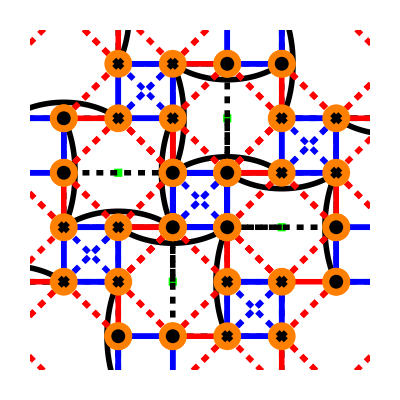

```mathematica
Graphics[Flatten[{vacc[vac],J3p[pointsr,boxposr],makejs[points,boxpos],arrows[points,boxpos]}],PlotRange->{{-3.5,2.5},{-3.5,2.5}}]
```

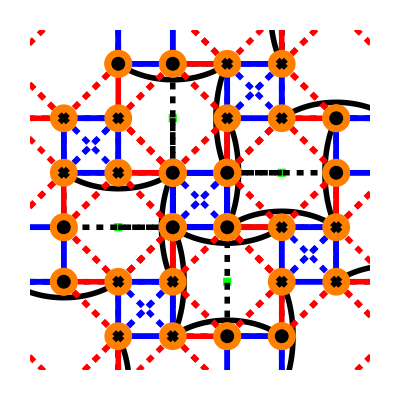

```mathematica
Graphics[Flatten[{vacc[vacr],J3p[points,boxpos],makejsr[pointsr,boxposr],arrows[pointsr,boxposr]}],PlotRange->{{-3.5,2.5},{-3.5,2.5}}]
```

```mathematica
lingr[pnt_,bx_]:={Dashing[None],Black,Thickness[lthick],Table[Table[Line[{pnt[[q]]+bx[[p]],bx[[p]]+pnt[[1+Mod[q+1,4]]]+bx[[q+1]]}],{q,Length[pnt]-1}],{p,Length[bx]}]};
boxes[pnt_,bx_]:={Black,Dashing[None],Thickness[lthick],Table[Table[box[Table[pnt[[n]]+bx[[p]],{n,Length[pnt]}],bx[[q]]],{p,Length[bx]}],{q,Length[bx]}]};
```

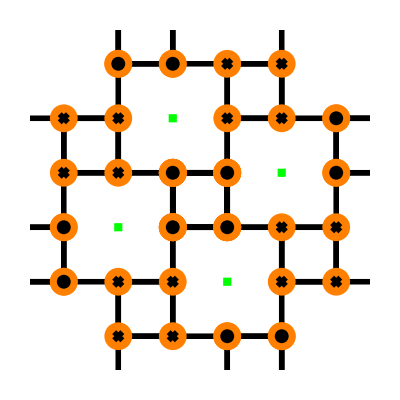

```mathematica
Graphics[Flatten[{lingr[pointsr,boxposr],boxes[pointsr,boxposr],arrows[pointsr,boxposr],vacc[vacr]}],PlotRange->{{-3.5,2.5},{-3.5,2.5}}]
```

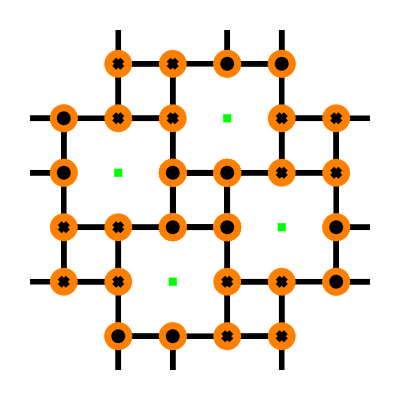

```mathematica
Graphics[Flatten[{lingr[points,boxpos],boxes[points,boxpos],arrows[points,boxpos],vacc[vac]}],PlotRange->{{-3.5,2.5},{-3.5,2.5}}]
```